```mathematica
Series[Exp[x], {x,0, 3}]
```

1+x+x^2/2+x^3/6+O[x]^4

```mathematica
Plot[x^2, {1.2, 20}]
```

Plot::pllim: Range specification {1.2,20} is not of the form {x, xmin, xmax}.

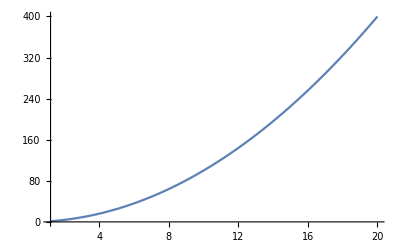

```mathematica
Plot[x^2,{x, 1.2,20}]
```

```mathematica
Range[1,3]
```

{1,2,3}

```mathematica
Exp[x]
```

ⅇ^x

```mathematica
Plot[Exp[x]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[Exp[x]]

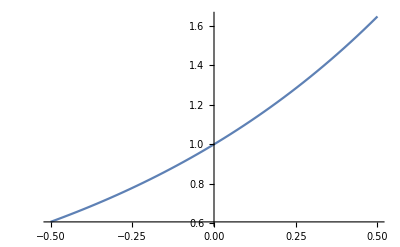

```mathematica
Plot[Exp[x], {x, -.5, .5}]
```

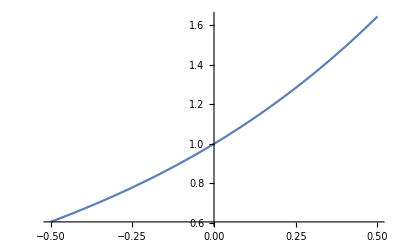

```mathematica
Plot[1+x+x^2/2+x^3/6,{x, -.5, .5}]
```

```mathematica
Series[Exp[x], {x, 0, 3}]
```

1+x+x^2/2+x^3/6+O[x]^4

```mathematica
Series[Exp[x], {x,0,3}]
```

1+x+x^2/2+x^3/6+O[x]^4

```mathematica
Plot[1+x+x^2/2+x^3/6, {x, -.5, .5}]
```

-Graphics-

```mathematica
Plot[Exp[x], {x, -.5, .5}]
```

-Graphics-

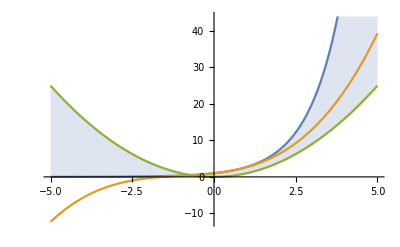

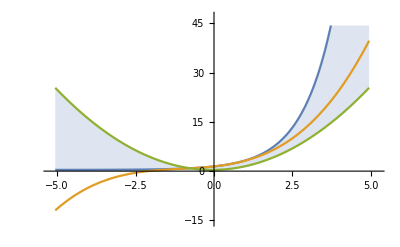

```mathematica
Plot[{Exp[x],1+x+x^2/2+x^3/6, x^2}, {x,-5,5}, Filling->{1->{3}}]
```

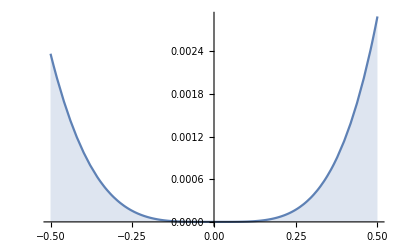

```mathematica
(*absolute measurement error: A-B where B=A*)

Plot[Exp[x]-(1+x+x^2/2+x^3/6), {x, -.5, .5}, Filling->Axis]
```

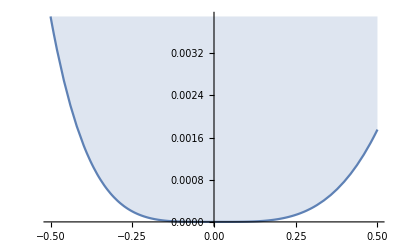

```mathematica
(*Относительная погрешность*)
Plot[(Exp[x]-(1+x+x^2/2+x^3/6))/Exp[x], {x, -.5, .5}, Filling->Top]
```